# CS 478

## Scott Leland Crossen

## Backpropagation Project

### Part 1

The code that implements the backpropagation rule is included with the submission of this project. It is written in Scala and follows the functional paradigm. Immutability is observed in all but the underlying learner.

### Part 2

The stopping criteria was met after 106 epochs

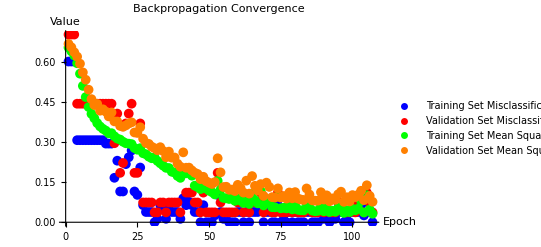

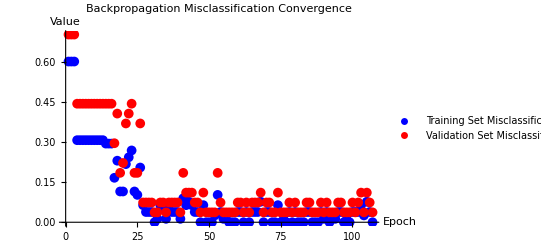

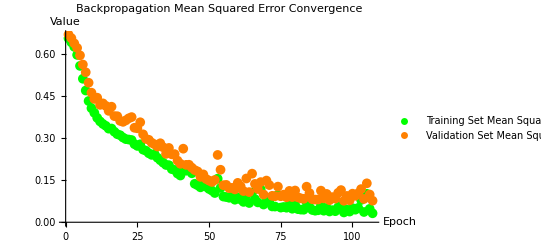

```mathematica
trainingSetAccuracies = {0.3974358974358974,0.3974358974358974,0.3974358974358974,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.7051282051282052,0.7051282051282052,0.7051282051282052,0.8333333333333334,0.7692307692307693,0.8846153846153846,0.8846153846153846,0.782051282051282,0.7564102564102564,0.7307692307692307,0.8846153846153846,0.8974358974358975,0.7948717948717948,0.9358974358974359,0.9615384615384616,0.9615384615384616,0.9615384615384616,1.0,0.9871794871794872,0.9358974358974359,0.9487179487179487,0.9871794871794872,0.9358974358974359,0.9615384615384616,0.9615384615384616,0.9615384615384616,0.9871794871794872,0.9102564102564102,0.9358974358974359,0.9230769230769231,0.9358974358974359,0.9615384615384616,0.9615384615384616,1.0,0.9358974358974359,1.0,1.0,1.0,0.9743589743589743,0.8974358974358975,0.9615384615384616,0.9871794871794872,0.9743589743589743,1.0,1.0,1.0,0.9615384615384616,0.9615384615384616,1.0,0.9615384615384616,1.0,0.9615384615384616,0.9615384615384616,0.9615384615384616,0.9230769230769231,1.0,0.9615384615384616,0.9615384615384616,1.0,1.0,0.9358974358974359,1.0,0.9743589743589743,1.0,0.9615384615384616,1.0,0.9615384615384616,1.0,1.0,1.0,0.9615384615384616,0.9615384615384616,1.0,1.0,1.0,0.9615384615384616,0.9871794871794872,0.9615384615384616,1.0,0.9743589743589743,0.9871794871794872,0.9615384615384616,0.9615384615384616,1.0,0.9743589743589743,1.0,0.9615384615384616,0.9615384615384616,0.9615384615384616,0.9358974358974359,0.9743589743589743,0.9230769230769231,0.9615384615384616,1.0};
validationSetAccuracies = {0.2962962962962963,0.2962962962962963,0.2962962962962963,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.7037037037037037,0.5925925925925926,0.8148148148148148,0.7777777777777778,0.6296296296296297,0.5925925925925926,0.5555555555555556,0.8148148148148148,0.8148148148148148,0.6296296296296297,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.8148148148148148,0.8888888888888888,0.8888888888888888,0.8888888888888888,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.8888888888888888,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.8148148148148148,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.8888888888888888,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.8888888888888888,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.8888888888888888,0.9629629629629629,0.8888888888888888,0.9259259259259259,0.9629629629629629};
trainingSetMse = {0.6552342423640292,0.6408325543950788,0.6249970155506919,0.5961843492992015,0.5569661074609347,0.5112211117424879,0.4692940462649557,0.4319777133044221,0.406263206447426,0.3898466997439498,0.3718614034132175,0.3592506294818036,0.35015131216194323,0.34347196398765495,0.3334433311687151,0.33391225401610874,0.32236986561553466,0.3136940996026338,0.30998251672930005,0.30178181550812766,0.29614397933524395,0.294603628276002,0.2928435954327163,0.2781751869020167,0.27196984417525927,0.2777205086842186,0.25872090196648595,0.2548391062458521,0.24578529366876473,0.24002781555045602,0.2431622245428669,0.2297525656696203,0.2209197368151618,0.21220068118513447,0.20404890123427105,0.20328991269747015,0.18934600188532102,0.18623074567591202,0.1736450653505924,0.16648513863207204,0.18756627498997974,0.18355366633172185,0.18865932094146667,0.17446612492181726,0.13706179786381661,0.1317805940234114,0.12439764084531926,0.14799960761782047,0.12627833691496199,0.1186051497550627,0.11287701162811586,0.10422109582212652,0.15525465394093835,0.12216422670913506,0.09150918136799036,0.0898526038162242,0.08722016864294241,0.09164905280049397,0.0803191964659962,0.08894495043292368,0.08119202359347849,0.07251953830250872,0.09619216240875236,0.06860327307616686,0.10595300428806631,0.08231810267260006,0.07079479116970851,0.11734881160170471,0.06317343705416899,0.08810882112654984,0.07753407111560928,0.056325032236430934,0.0559207402499614,0.09729490077204546,0.05223505200686057,0.054386002057460046,0.051856740148711555,0.061584927376159,0.04820491888390029,0.061811408145383724,0.0466933968777776,0.04504899661136008,0.04466552915389915,0.07027807346804667,0.05475353622944006,0.04369481913263928,0.04119605472427659,0.042769188355520585,0.059631009668108824,0.04115358729148645,0.05102547109142463,0.038379067019753625,0.0430727487294689,0.03943949531049421,0.05333022500115838,0.06014943578441246,0.03497206695710427,0.04498848082782567,0.038107045911182025,0.050231811973668106,0.044813552461209015,0.051194373039814126,0.07930255959738142,0.03656451191823308,0.10124386696466808,0.047692584317987306,0.03195500913062534};
validationSetMse = {0.6686474191835949,0.6557840431343953,0.6372566764419858,0.6209663489780133,0.5944675663781497,0.561825515877718,0.5343168398247629,0.49700161390277925,0.4615941510128583,0.43922219488416386,0.44374057366048564,0.4182105284728457,0.4235009385334716,0.4146014278055962,0.3968611009608179,0.41160506057212415,0.3781307544531358,0.3776984513593004,0.3612365180224738,0.3576761356076088,0.3631195682935622,0.370235282279283,0.37455104044569093,0.33659703492037824,0.3348084439848566,0.3561747928664723,0.31320787510185283,0.29719254699423675,0.2936617622754136,0.28314764513462737,0.27764384217274385,0.2697841099277731,0.28138098811267104,0.2669877137565196,0.24360442762413068,0.26474562049224515,0.24197381334443627,0.2427002909027579,0.21950750747233483,0.20823234711520747,0.2620651495511065,0.20444738374253354,0.20480953369851845,0.19433050299072308,0.1858237749486254,0.18110443713777993,0.16168437685953604,0.17046116154113913,0.15392492652783285,0.14838235833093275,0.14345905093065062,0.1504851644320455,0.2397775887838155,0.18701300080358094,0.131959983586604,0.13303930241610348,0.12170800016345762,0.12247022120156587,0.11695783926325334,0.14028458052138223,0.1283414076441494,0.11109206040139864,0.15591540808366336,0.10741695393170946,0.1730806607362933,0.13657036103459166,0.11859740446532799,0.14294959858007256,0.09892379027380287,0.14847433440851004,0.13242671814196785,0.09412462514401267,0.09279077494793037,0.12689100637794,0.09259480889956848,0.09836597357485827,0.08890102151594609,0.11169399176477708,0.08968971476000538,0.11301370621819942,0.08877557594228823,0.0852386640219342,0.08351214403494868,0.12670524330644076,0.10405290982276366,0.08212690183520038,0.08075827193389465,0.08109481708315529,0.11256304280913484,0.08518609112124842,0.10088469469475442,0.07863360254895334,0.08950103923907005,0.08425622829337398,0.10472857043788703,0.11457009983644605,0.07655436385138993,0.09373728302264087,0.0781314166547198,0.10180021336823504,0.09421506050961997,0.10307165033903505,0.1180377294419575,0.08292056397157233,0.13867913251526387,0.09880917624373617,0.07679263059027847};
range = Range[Length[trainingSetAccuracies]];

ListPlot[{Transpose[{range,1-trainingSetAccuracies}],Transpose[{range,1-validationSetAccuracies}],Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}]}, AxesLabel->{Style["Epoch", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Convergence", Black], PlotStyle->{Blue, Red, Green, Orange},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Misclassification", "Validation Set Misclassification","Training Set Mean Squared Error", "Validation Set Mean Squared Error"}]

ListPlot[{Transpose[{range,1-trainingSetAccuracies}],Transpose[{range,1-validationSetAccuracies}]}, AxesLabel->{Style["Epoch", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Misclassification Convergence", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Misclassification", "Validation Set Misclassification"}]

ListPlot[{Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}]}, AxesLabel->{Style["Epoch", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Mean Squared Error Convergence", Black], PlotStyle->{Green, Orange},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Mean Squared Error", "Validation Set Mean Squared Error"}]
```

### Part 3

For the purposes of this project, the stopping criteria is considered to be fulfilled when a continuous 5 epochs of the training set improved the weight vector by less than a cumulative 1.5 (half of the amount of features) across the feature vector times the learning constant. This value was chosen so that a smaller learning constant would be taken into account and allow the algorithm to arrive at a more precise result. Moreover, under this value a larger feature set allows more ability for the algorithm to change before stopping. This is why the overall equation is written this way.

The results show that the learning constant doesn’t really affect the amount of time it takes to train the perceptron. Data is given below showing the amount of epochs it takes to converge vs the learning constant. For a given single learning constant it was observed that a larger learning constant resulted in more sporadic changes in the weight vector whereas a smaller learning constant was more gradual in achieving the optimal solution. This of course is probably a result of the more-volatile nature of a larger training constant.

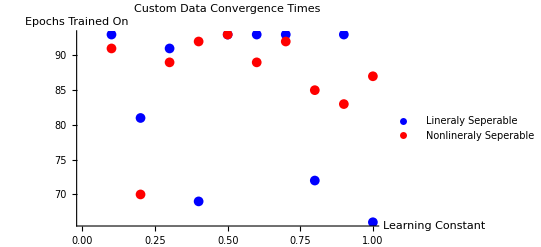

```mathematica
data={{.1,93,91},{.2,81,70},{.3,91,89},{.4,69,92},{.5,93,93},{.6,93,89},{.7,93,92},{.8,72,85},{.9,93,83},{1,66,87}};
ListPlot[{Transpose[{Transpose[data][[1]],Transpose[data][[2]]}],Transpose[{Transpose[data][[1]],Transpose[data][[3]]}]}, AxesLabel->{Style["Learning Constant", Black],Style["Epochs Trained On", Black]}, PlotLabel->Style["Custom Data Convergence Times", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Lineraly Seperable", "Nonlineraly Seperable"}]
```

### Part 4

The below plots show the two different solutions to the above ARFF files. The first shows a correct separation of the data and the second shows a poor separation of the data (because it is not linearly separable)

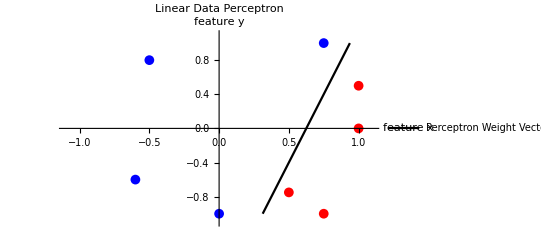

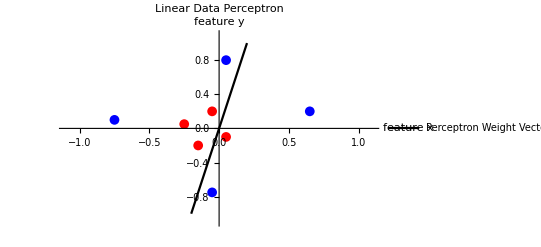

```mathematica
Show[
plotBinaryPerceptronData[{{{-.6,-.6},{-.5,.8},{0,-1},{.75,1}},{{1,0},{.5,-.75},{1,.5},{.75,-1}}}],
plotBinaryPerceptronLine[-0.16,0.05000000000000001,0.1]
]
Show[
plotBinaryPerceptronData[{{{.05,.8},{.65,.2},{-.05,-.75},{-.75,.1}},{{-.05,.2},{-.25,.05},{-.15, -.2},{.05,-.1}}}],
plotBinaryPerceptronLine[-0.05000000000000002,0.009999999999999995,0.0]
]
```

### Part 5

For a perceptron that is forced to train on all the data we found an accuracy in the 90s. The plots below show the results for 5 trials.

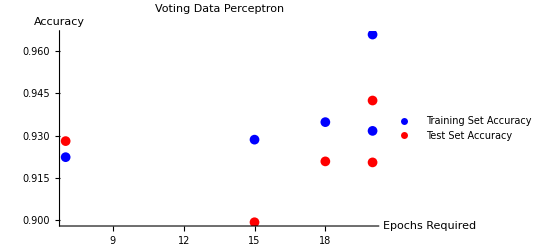

The average amount of epochs trained on was 16.

The average training accuracy was 0.936646

The average testing accuracy was 0.92223

```mathematica
accuracy = {{15,0.9285714285714286,0.8992805755395683},{20,0.9316770186335404,0.9205035971223022},{7,0.922360248447205,0.9280575539568345},{18,0.9347826086956522,0.920863309352518},{20,0.9658385093167702,0.9424460431654677}};
ListPlot[{Transpose[{accuracy[[All,1]],accuracy[[All, 2]]}],Transpose[{accuracy[[All,1]],accuracy[[All, 3]]}]}, AxesLabel->{Style["Epochs Required", Black],Style["Accuracy", Black]}, PlotLabel->Style["Voting Data Perceptron", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average amount of epochs trained on was ", N[Mean[accuracy[[All,1]]]]]
Print["The average training accuracy was ", N[Mean[accuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[accuracy[[All,3]]]]]
```

For this  data set a good stopping criteria was determined to be when the perceptron reached 5 successive iterations of it’s data set with no significant increase in the weight vector. A significant increase is considered to be when the summed changed in the weight vector is more than 1/2 times the number of features times the training constant. The logic behind this algorithm is explained more fully in part 3 of this project.

The final weight vector for a perceptron with a test accuracy of 96 % turns out to be {0.0, 0.47336482815648373, 1.1834120703912094, -1.6567768985476934, 0.0, 0.23668241407824187, -0.23668241407824187, -0.23668241407824187, 0.9467296563129675, -0.47336482815648373, 0.7100472422347256, -0.47336482815648373, 0.47336482815648373, -0.23668241407824187, 0.9467296563129675, -0.23668241407824187, 0.47336482815648373}.
According to this data, there is a slight offset (bias) in the data. Moreover, the 3rd and 4th features seem to be the most influential with the 1st and 5th features being least influential. It’s important to note that not all returned weight vectors had a bias. The most-accurate ones all did though. Note that the longer the perceptron was allowed to train the more accurate it tended to be. This is best shown by the upward-sloping trend in the above plot.

Most influential features: 3, 4
Least Influential features: 1, 5

Below is a plot of average misclassification rate vs epochs elapsed. It would appear that not much improvement happens after the first epoch. Though the graph below would have stopped much earlier than 50 epochs, I suspended the halting criteria to demonstrate the misclassification rate over a longer period. Again, I suspect that the misclassification rate would not be so noisy if I allowed for a smaller time frame. More than that, but it is likely that my perceptron was able to accurately train itself after one epoch and continuing the training was just overkill.

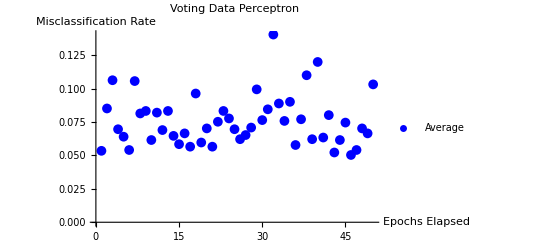

```mathematica
data1 =Transpose[{Range[100],{0.06521739130434778,0.04347826086956519,0.10248447204968947,0.0496894409937888,0.04658385093167705,0.0496894409937888,0.03416149068322982,0.06521739130434778,0.10248447204968947,0.03416149068322982,0.04037267080745344,0.06211180124223603,0.09316770186335399,0.05900621118012417,0.03105590062111796,0.06521739130434778,0.03105590062111796,0.04658385093167705,0.05590062111801242,0.04347826086956519,0.03416149068322982,0.04347826086956519,0.0714285714285714,0.03416149068322982,0.07763975155279501,0.08074534161490687,0.03105590062111796,0.04658385093167705,0.04347826086956519,0.037267080745341574,0.05590062111801242,0.23291925465838514,0.04037267080745344,0.09316770186335399,0.04037267080745344,0.05590062111801242,0.05590062111801242,0.15527950310559002,0.08695652173913049,0.33229813664596275,0.037267080745341574,0.04658385093167705,0.04347826086956519,0.04658385093167705,0.03416149068322982,0.037267080745341574,0.0496894409937888,0.04347826086956519,0.03105590062111796,0.06211180124223603,0.08074534161490687,0.06211180124223603,0.04658385093167705,0.05590062111801242,0.09627329192546585,0.05900621118012417,0.06211180124223603,0.04037267080745344,0.05900621118012417,0.04347826086956519,0.04037267080745344,0.04347826086956519,0.07453416149068326,0.052795031055900665,0.04037267080745344,0.06521739130434778,0.09627329192546585,0.037267080745341574,0.052795031055900665,0.052795031055900665,0.28881987577639756,0.04347826086956519,0.08074534161490687,0.04347826086956519,0.07763975155279501,0.20186335403726707,0.09627329192546585,0.05590062111801242,0.052795031055900665,0.037267080745341574,0.04037267080745344,0.03416149068322982,0.13043478260869568,0.08074534161490687,0.052795031055900665,0.037267080745341574,0.052795031055900665,0.18322981366459623,0.03105590062111796,0.13354037267080743,0.07763975155279501,0.052795031055900665,0.1273291925465838,0.04037267080745344,0.03416149068322982,0.037267080745341574,0.05590062111801242,0.10869565217391308,0.06211180124223603,0.04037267080745344}}];
data2 =Transpose[{Range[100],{0.05900621118012417,0.1708074534161491,0.06211180124223603,0.04347826086956519,0.08695652173913049,0.052795031055900665,0.0714285714285714,0.1149068322981367,0.06832298136645965,0.06832298136645965,0.1645962732919255,0.05900621118012417,0.08695652173913049,0.04658385093167705,0.06521739130434778,0.0496894409937888,0.0496894409937888,0.10248447204968947,0.0496894409937888,0.09006211180124224,0.052795031055900665,0.052795031055900665,0.06832298136645965,0.09006211180124224,0.0496894409937888,0.0496894409937888,0.0496894409937888,0.052795031055900665,0.17391304347826086,0.07763975155279501,0.18012422360248448,0.10869565217391308,0.11180124223602483,0.04037267080745344,0.08385093167701863,0.04347826086956519,0.0993788819875776,0.05590062111801242,0.04347826086956519,0.06211180124223603,0.05590062111801242,0.052795031055900665,0.05900621118012417,0.052795031055900665,0.06521739130434778,0.04658385093167705,0.04658385093167705,0.05590062111801242,0.04037267080745344,0.1428571428571429,0.052795031055900665,0.052795031055900665,0.06521739130434778,0.0993788819875776,0.052795031055900665,0.08695652173913049,0.052795031055900665,0.052795031055900665,0.0496894409937888,0.11180124223602483,0.13975155279503104,0.0714285714285714,0.052795031055900665,0.037267080745341574,0.05590062111801242,0.06521739130434778,0.052795031055900665,0.037267080745341574,0.08385093167701863,0.2857142857142857,0.052795031055900665,0.0496894409937888,0.05590062111801242,0.09316770186335399,0.14596273291925466,0.1925465838509317,0.06521739130434778,0.05900621118012417,0.0496894409937888,0.19875776397515532,0.05900621118012417,0.04347826086956519,0.09627329192546585,0.04037267080745344,0.10559006211180122,0.04658385093167705,0.052795031055900665,0.06211180124223603,0.0714285714285714,0.052795031055900665,0.1273291925465838,0.09316770186335399,0.06211180124223603,0.05590062111801242,0.06521739130434778,0.3012422360248447,0.052795031055900665,0.04037267080745344,0.052795031055900665,0.04658385093167705}}];
data3 =Transpose[{Range[100],{0.04658385093167705,0.06211180124223603,0.06211180124223603,0.11180124223602483,0.09316770186335399,0.06211180124223603,0.05590062111801242,0.05900621118012417,0.0496894409937888,0.09316770186335399,0.0714285714285714,0.07763975155279501,0.06211180124223603,0.05900621118012417,0.0714285714285714,0.0714285714285714,0.08385093167701863,0.0993788819875776,0.05900621118012417,0.0496894409937888,0.03416149068322982,0.05900621118012417,0.13354037267080743,0.13975155279503104,0.0496894409937888,0.04347826086956519,0.0496894409937888,0.13975155279503104,0.04658385093167705,0.08385093167701863,0.052795031055900665,0.1211180124223602,0.10559006211180122,0.10248447204968947,0.05900621118012417,0.05590062111801242,0.08695652173913049,0.0496894409937888,0.05900621118012417,0.04037267080745344,0.06211180124223603,0.1708074534161491,0.04347826086956519,0.03416149068322982,0.06832298136645965,0.07453416149068326,0.03105590062111796,0.13354037267080743,0.07763975155279501,0.1211180124223602,0.08695652173913049,0.18322981366459623,0.037267080745341574,0.04658385093167705,0.08385093167701863,0.11180124223602483,0.07453416149068326,0.07453416149068326,0.1273291925465838,0.08074534161490687,0.04658385093167705,0.09627329192546585,0.06832298136645965,0.04658385093167705,0.06211180124223603,0.06832298136645965,0.0993788819875776,0.0496894409937888,0.05900621118012417,0.04347826086956519,0.0714285714285714,0.04347826086956519,0.09627329192546585,0.05590062111801242,0.10559006211180122,0.06832298136645965,0.06211180124223603,0.04658385093167705,0.06521739130434778,0.06832298136645965,0.10869565217391308,0.06521739130434778,0.04658385093167705,0.07763975155279501,0.05590062111801242,0.21118012422360244,0.05900621118012417,0.06521739130434778,0.1863354037267081,0.06211180124223603,0.05900621118012417,0.10559006211180122,0.1273291925465838,0.052795031055900665,0.3571428571428571,0.10248447204968947,0.0496894409937888,0.1149068322981367,0.05900621118012417,0.04347826086956519}}];
data4 =Transpose[{Range[100],{0.03416149068322982,0.05900621118012417,0.24844720496894412,0.052795031055900665,0.052795031055900665,0.0496894409937888,0.10869565217391308,0.09316770186335399,0.1428571428571429,0.04037267080745344,0.06832298136645965,0.07453416149068326,0.1149068322981367,0.06832298136645965,0.05900621118012417,0.08385093167701863,0.05900621118012417,0.05590062111801242,0.05590062111801242,0.08385093167701863,0.10869565217391308,0.13043478260869568,0.06211180124223603,0.06211180124223603,0.1211180124223602,0.06832298136645965,0.07453416149068326,0.06211180124223603,0.17391304347826086,0.05900621118012417,0.0496894409937888,0.17701863354037262,0.0993788819875776,0.0496894409937888,0.1490683229813664,0.0714285714285714,0.08695652173913049,0.2080745341614907,0.052795031055900665,0.03105590062111796,0.06832298136645965,0.0714285714285714,0.052795031055900665,0.06211180124223603,0.04037267080745344,0.037267080745341574,0.07453416149068326,0.052795031055900665,0.1149068322981367,0.11801242236024845,0.10869565217391308,0.05590062111801242,0.03416149068322982,0.07453416149068326,0.06211180124223603,0.26086956521739135,0.05590062111801242,0.0496894409937888,0.03105590062111796,0.052795031055900665,0.1645962732919255,0.05900621118012417,0.037267080745341574,0.052795031055900665,0.05590062111801242,0.1149068322981367,0.06832298136645965,0.08074534161490687,0.0993788819875776,0.20496894409937894,0.07763975155279501,0.0496894409937888,0.05590062111801242,0.08385093167701863,0.05590062111801242,0.05900621118012417,0.0496894409937888,0.05590062111801242,0.037267080745341574,0.04037267080745344,0.07453416149068326,0.05900621118012417,0.05900621118012417,0.04037267080745344,0.04037267080745344,0.04347826086956519,0.07453416149068326,0.06521739130434778,0.05590062111801242,0.037267080745341574,0.10248447204968947,0.06521739130434778,0.04037267080745344,0.04347826086956519,0.0496894409937888,0.052795031055900665,0.03416149068322982,0.04037267080745344,0.09316770186335399,0.11180124223602483}}];
data5 =Transpose[{Range[100],{0.06211180124223603,0.09006211180124224,0.05590062111801242,0.09006211180124224,0.04037267080745344,0.05590062111801242,0.2577639751552795,0.07453416149068326,0.052795031055900665,0.0714285714285714,0.06521739130434778,0.0714285714285714,0.05900621118012417,0.09006211180124224,0.06521739130434778,0.06211180124223603,0.05900621118012417,0.17701863354037262,0.07763975155279501,0.08385093167701863,0.052795031055900665,0.09006211180124224,0.08074534161490687,0.06211180124223603,0.0496894409937888,0.06832298136645965,0.1211180124223602,0.052795031055900665,0.05900621118012417,0.12422360248447206,0.08385093167701863,0.06211180124223603,0.08695652173913049,0.09316770186335399,0.11801242236024845,0.06211180124223603,0.05590062111801242,0.08074534161490687,0.06832298136645965,0.13354037267080743,0.09316770186335399,0.05900621118012417,0.06211180124223603,0.11180124223602483,0.1645962732919255,0.05590062111801242,0.06832298136645965,0.06521739130434778,0.06832298136645965,0.0714285714285714,0.07763975155279501,0.15527950310559002,0.12422360248447206,0.05900621118012417,0.05900621118012417,0.052795031055900665,0.17391304347826086,0.09627329192546585,0.10869565217391308,0.08074534161490687,0.28260869565217395,0.05900621118012417,0.0496894409937888,0.06211180124223603,0.08385093167701863,0.04347826086956519,0.06521739130434778,0.052795031055900665,0.05590062111801242,0.16149068322981364,0.10869565217391308,0.08695652173913049,0.07453416149068326,0.05590062111801242,0.07453416149068326,0.23913043478260865,0.06521739130434778,0.05590062111801242,0.06521739130434778,0.06211180124223603,0.07453416149068326,0.08695652173913049,0.07763975155279501,0.06521739130434778,0.06211180124223603,0.05590062111801242,0.07763975155279501,0.06211180124223603,0.08385093167701863,0.0714285714285714,0.08074534161490687,0.05900621118012417,0.06832298136645965,0.08385093167701863,0.07453416149068326,0.0496894409937888,0.052795031055900665,0.05590062111801242,0.21739130434782605,0.06832298136645965}}];
data = (data1+data2+data3+data4+data5)/5;
ListPlot[data[[1;;50,All]], AxesLabel->{Style["Epochs Elapsed", Black],Style["Misclassification Rate", Black]}, PlotLabel->Style["Voting Data Perceptron", Black], PlotStyle->Blue,PlotMarkers-> {●,10}, PlotLegends->{"Average"}]
```

### Part 6

For this part I created two different perceptrons to solve the iris data set. The two perceptrons are the same as described in the problem statement. The perceptron described in part (a) is called a individual-test perceptron. The perceptron described in part (b) is called the matched-pairs perceptron. Each implementation can be found in the code included in the submission of this project.

Each perceptron was allowed to train on 70% of the data and then test the remaining 30%. Only one epoch was used in order to demonstrate baseline viability. Stopping criteria was found not to affect the overall results and so was not included for consistency.

As shown by the data, the matched pairs perceptron achieved a higher and more stable accuracy compared to the individual perceptron model. In fact, it would appear as if in almost every case the matched pairs model performed better than the individual selection model. Average accuracy is included for reference. I propose that the results are because the matched pairs experiment is a more defined experiment - The machine only needs to separate between two sets of data rather than 3 at a time. For example, it is conceivable to have three sets of data with one set in the middle. A individually-selecting perceptron would not be able to separate this middle portion from the two outside portions whereas the matched-pairs perceptron could. This is why the matched-pairs perceptron is likely better.

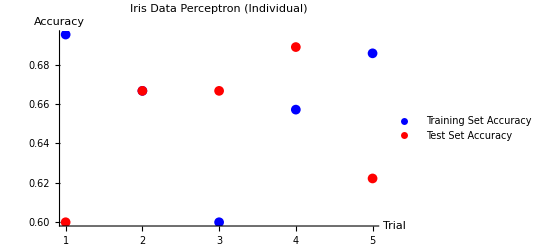

The average training accuracy was 0.660952

The average testing accuracy was 0.648889

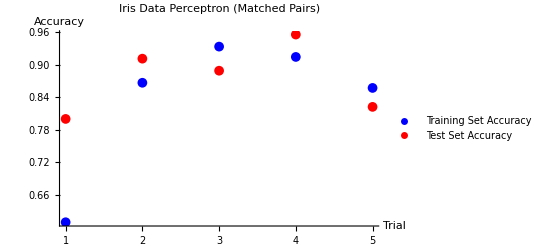

The average training accuracy was 0.83619

The average testing accuracy was 0.875556

```mathematica
IndividualAccuracy = {{1,0.6952380952380952,0.6},{2,0.6666666666666666,0.6666666666666666},{3,0.6,0.6666666666666666},{4,0.6571428571428571,0.6888888888888889},{5,0.6857142857142857,0.6222222222222222}};
matchedPairsAccuracy = {{1,0.6095238095238096,0.8},{2,0.8666666666666667,0.9111111111111111},{3,0.9333333333333333,0.8888888888888888},{4,0.9142857142857143,0.9555555555555556},{5,0.8571428571428571,0.8222222222222222}};
ListPlot[{Transpose[{IndividualAccuracy[[All,1]],IndividualAccuracy[[All, 2]]}],Transpose[{IndividualAccuracy[[All,1]],IndividualAccuracy[[All, 3]]}]}, AxesLabel->{Style["Trial", Black],Style["Accuracy", Black]}, PlotLabel->Style["Iris Data Perceptron (Individual)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average training accuracy was ", N[Mean[IndividualAccuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[IndividualAccuracy[[All,3]]]]]
ListPlot[{Transpose[{matchedPairsAccuracy[[All,1]],matchedPairsAccuracy[[All, 2]]}],Transpose[{matchedPairsAccuracy[[All,1]],matchedPairsAccuracy[[All, 3]]}]}, AxesLabel->{Style["Trial", Black],Style["Accuracy", Black]}, PlotLabel->Style["Iris Data Perceptron (Matched Pairs)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average training accuracy was ", N[Mean[matchedPairsAccuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[matchedPairsAccuracy[[All,3]]]]]
```